```mathematica
(*define paramteres here*)
T=  200;(*unit in K*)
n= 6; m=5;(*SWCNT chirality*)
Nr = 1;
hbargamma=5*1.6/1000;(*scarttering in meV,convert to J order e-19*)
Nk=500;

(*define constants here*) 
a = 2.46;(*graphene primitive vector length unit A*)
ga = 2.9*1.6;(*graphene hopping energy in eV,convert to J order: e-19*)
eChar= 1.6; (*unit C, e-19*)
hbar= 1.05;(*SI unit order e-34*)
pi4eps0=4*Pi*8.854;(*SI unit C^2/Nm^2 order e-12*)
kappa= 3;

(*itermediate terms*)
Ch=a*Sqrt[n^2+m^2+n*m];(*unit A*)
L = Sqrt[3]/Nr*Ch;(*unit cell length, unit A*)
kc = Pi/L;(*first Broullie zone, unit 1/A*)
step=2*kc/Nk;
n1tk[n_]:=-kc+n*step;
n2tk[n_]:=-kc+n*step;
dcv = 3*eChar/(4*Pi)*Ch;(*unit C*A, order e-19 *)
Ec[n_]:=ga*Sqrt[3]*a/2*Sqrt[(2*Pi/(3*Ch))^2+(n1tk[n])^2];(*unit J, e-19*)
Ev[k_]:=-Ec[k];(*unit J, e-19*)

(*kx[n1_]:=a*Pi*(n+m)/(Sqrt[3]*Ch^2)+n1tk[n1]*Sqrt[3]*(m-n)/(2*Sqrt[m^2+n^2-m*n]);
ky[n1_]:=4*Pi/(3*a)+a*Pi*(n-m)/(3*Ch^2)+n1tk[n1]*(m+n)/(2*Sqrt[m^2+n^2-m*n]);
Ec[n1_]:=ga*Sqrt[1+4*Cos[Sqrt[3]*a*kx[n1]/2]Cos[a*ky[n1]/2]+4*(Cos[a*ky[n1]/2]^2)]*)

I0gen[n_]:=BesselI[0,L*Abs[n1tk[n]]/(2*Pi)];(*unit 1*)
K0gen[n_]:=BesselK[0,L*Abs[n1tk[n]]/(2*Pi)];(*unit 1*)
FF2[k_,q_,b_]:=0.5*(1+b*((2*Pi/(3*Ch))^2+k^2+k*q)/Sqrt[((2*Pi/(3*Ch))^2+k^2)*((2*Pi/(3*Ch))^2+(k+q)^2)]);(*unit 1*)
pI[k_,q_]:=2*(-2)*FF2[k,q,-1]/(Ec[k+q]-Ev[k]);(*unit 1/J, e19. K&K' brought in 2, cv exchange brought in the other 2*)
PI[q_]:= 2*Pi*Sum[pI[k,q],{k,-kc,kc,step}]*step;(*unit 1/JA, e19*)
I0List=Array[I0gen,Nk];
K0List=Array[K0gen,Nk];
epsilon[n_]:=1+0.001*2*eChar^2/(kappa*pi4eps0)*I0List[[n]]*K0List[[n]]*PI[n1tk[n]];(*unit 1*)
epsilongen[n_]:=epsilon[n];

epsilonList=Array[epsilongen,Nk];
v[n1_,n2_,b_]:=N[1000*2*eChar^2/(kappa*pi4eps0)*I0List[[n2]]*K0List[[n2]]*FF2[n1tk[n1],n2tk[n2],b]];(*unit JA order e-19*)
V[n1_,n2_,b_]:=N[If[n2==Nk/2,0,v[n1,n2,b]/epsilonList[[n2]]]];(*unit JA order e-19*)
```

```mathematica
V1gen[n1_,n2_]:=V[n1,n2,1];
V2gen[n1_,n2_]:=V[n1,n2,-1];

(*generate matrix V for multiple use*)
VV1=Array[V1gen,{Nk,Nk}];
VV2=Array[V2gen,{Nk,Nk}];
```

```mathematica
(*calculate electron distribution*)
fcgen[n_]:=If[Abs[n-Nk/2]≤0*Nk/2,1,0];
hvgen[n_]:=If[Abs[n-Nk/2]≤0*Nk/2,1,0];
fc=Array[fcgen,Nk];
hv=Array[hvgen,Nk];
```

```mathematica
(*band renormalization with full valence band and empty conducting band*)
(*rEv[k_]:=Ev[k]-1/(2*Pi)*Sum[V[k,q,1]-V[k,q,-1],{q,-kc,kc,step}]*step;*)
rEv[n_]:=Ev[n]-1/(2*Pi)*Sum[VV1[[n,n2]]-VV2[[n,n2]],{n2,1,Nk}]*step;(*unit J, order e-19*)
(*energy renormalization with e-h interaction*)(*need to change fc[n] to fc[n+q]*)
reEc[n_]:= Ec[n]-1/(2*Pi)*Sum[(VV1[[n,n2]]-VV2[[n,n2]])*fc[[Mod[n2+n+Nk/2-1,Nk]+1]],{n2,1,Nk}]*step;(*unit J, order e-19*)
reEv[n_]:= rEv[n]+1/(2*Pi)*Sum[(VV1[[n,n2]]-VV2[[n,n2]])*hv[[Mod[n2+n+Nk/2-1,Nk]+1]],{n2,1,Nk}]*step;(*unit J, order e-19*)
reEcList=Array[reEc,Nk];
reEvList=Array[reEv,Nk];
```

```mathematica
(*calculate matrix elements*)
(*diagonal term function*)
hbargamma = 10*1.6/1000;
Mdia[n_]:=-(reEcList[[n]]-reEvList[[n]]-I hbargamma)/hbar;(*unit J/hbar, e-19*)
(*non diagonal term function*)
Mnond[n1_,n2_]:=(1-fc[[n1]]-hv[[n1]])*VV1[[n1,Mod[n2-n1+Nk/2-1,Nk]+1]]/(2*Pi*hbar)*step;(*unit J/hbar, e-19*)
(*calculate non-trival term*)
Ygen[n_]:=(fc[[n]]+hv[[n]]-1)/hbar*dcv;(*unit CA/hbar, order e-19*)
Mgen[n1_,n2_]:=If[n1==n2,Mdia[n1],Mnond[n1,n2]];
M=Array[Mgen,{Nk,Nk}];
Y=Array[Ygen,Nk];
X[hbaromega_]:=LinearSolve[M+IdentityMatrix[Nk]*hbaromega*1.6/hbar,Y];
```

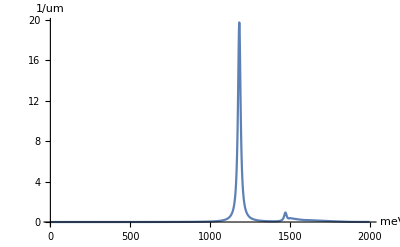

```mathematica
(*Sus[i_]:=Im[Total[X[i/1000]]];*)
(*unit correction *)
narea=1/1000;(*1/A^2*)
nb=1.5;
c=3;(*m/s e8*)
iteV[i_]:=i/1000;
Sus[i_]:=Im[Total[X[i]]]*dcv*narea/(Nk*L*pi4eps0)*1000; (*unit 1*)
epsIm[i_]:=Sus[iteV[i]]*4*Pi;
absp[i_]:=Sus[iteV[i]]*4*Pi*iteV[i]/(hbar*3*nb*1.6)*10;(*unit e6*)
ListLinePlot[Array[absp,2000],PlotRange->All,AxesLabel->{meV,1/um}]
```

```mathematica
Show[%450,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

-Graphics-

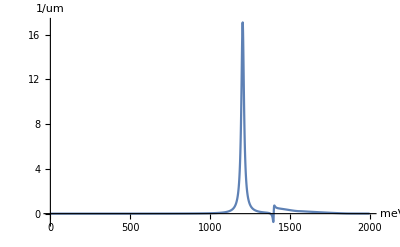

```mathematica
Show[%432,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

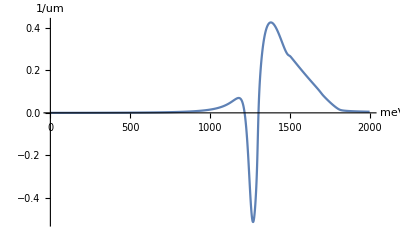

```mathematica
Show[%415,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

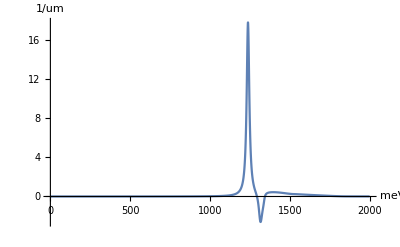

```mathematica
Show[%398,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

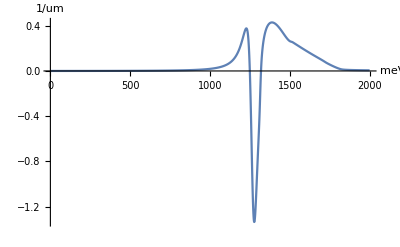

```mathematica
Show[%381,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

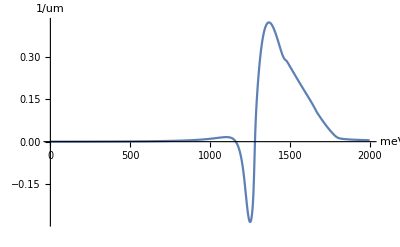

```mathematica
Show[%364,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

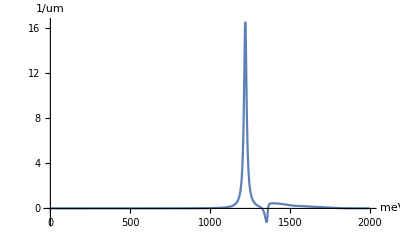

```mathematica
Show[%347,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

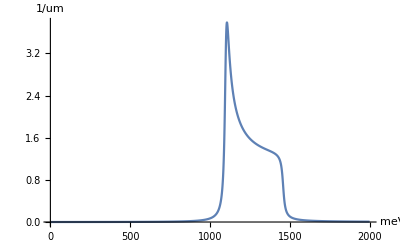

```mathematica
Show[%329,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

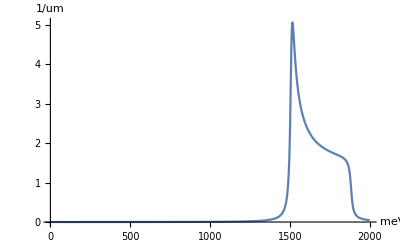

```mathematica
Show[%315,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

```mathematica
Show[%316,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

-Graphics-